```mathematica
Quit[];
```

```mathematica
η=0.8;
q=0.36;
Δt=19767^-0.28;
ΔtNight=1.16;
f=8.3;
fNight=2.1;
λ1=400*10^-9;
λ2=700*10^-9;
k=0.035;
l=57;
d=3*10^-6;
const=1/(6.63*10^-34*2.998*10^8);
Cbar=0.4;

λTest=507*10^-9;
```

```mathematica
(*Stavenga et al 1993*)
(*Vitamin A1 rhodopsin constants*)
a0α=380;
a1α=6.09;
a0β=247;
a1β=3.59;
Aα=1;
Aβ=0.29;

(*Peak Absorabance Wavelengths*)
λmaxα=500*10^-9; (*μm*)
λmaxβ=350*10^-9;(*μm*)
(*μm*)
```

```mathematica
xα[λ_]:= Log[λ/λmaxα];
xβ[λ_]:= Log[λ/λmaxβ];
(*SSH template calculations*)
α[λ_]:= Aα*Exp[-a0α*xα[λ]^2*(1+a1α*xα[λ]+(3/8)*a1α^2*(xα[λ])^2)];
β[λ_]:= Aβ*Exp[-a0β*xβ[λ]^2*(1+a1β*xβ[λ]+(3/8)*a1β^2*(xβ[λ])^2)];
A[λ_]:= α[λ]+β[λ];
```

```mathematica
(*Bowker et al 1985*)
λDaylight=Import[FileNameJoin[{NotebookDirectory[],"daylightRadiance.csv"}]];
IλDaylight=Interpolation[λDaylight]
λStarlight=Import[FileNameJoin[{NotebookDirectory[],"starlightRadiance.csv"}]];
IλStarlight=Interpolation[λStarlight]
λMoonlight=Import[FileNameJoin[{NotebookDirectory[],"moonlightRadiance.csv"}]];
IλMoonlight=Interpolation[λMoonlight]
spreadConstant=Import[FileNameJoin[{NotebookDirectory[],"spreadFunction.csv"}]];
s=Interpolation[spreadConstant]
```

InterpolatingFunction[{{0.4036, 0.7917}}, <>]

InterpolatingFunction[{{0.3169, 0.7914}}, <>]

InterpolatingFunction[{{0.3041, 0.9079}}, <>]

InterpolatingFunction[{{0.001, 0.006}}, <>]

```mathematica
minpupil=0.001; maxpupil=0.006;
pupilValues=Array[# &,25,{minpupil,maxpupil}];

Δρl[λ_,P_]:= λ/P;
Δρr[λ_,P_]:=λ/(2*P);
Δρ2[λ_,P_]:=(Δρl[λ,P])^2+0.38*(Δρr[λ,P])^2;
Δϕ[λ_,P_]:= λ/(2*P);

Ml[v_,P_]:=Exp[-(v/(20.9-2.1*P))^(1.3-0.07*P)];
Mr[v_,λ_,P_]:=Exp[-1.35*v^2*Δρ2[λ,P]];

vs[λ_,P_]:=1/(2*Δϕ[λ,P]);

P2[v_]:=1/(v^2);
k2=2*NIntegrate[v*P2[v],{v,0,Infinity}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::zeroregion: Integration region {{0., 0}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {8.1933649966303075080653271703138185060184363358617443426489735027×10^-76}. NIntegrate obtained 233.811 and 8.74984 for the integral and error estimates.

```mathematica
HDaylight={};
For[i=1,i≤ Length[pupilValues],i++,
DD=pupilValues[[i]];
NDaylight[λ_]:= η*Δt*(π/4)^2*DD^2*(d/(f*DD))^2*((IλDaylight[λ*10^6]*λ*10^6*10)*λ*const)*(1-Exp[-k*A[λ]*l]);

gD[v_,λ_]:=(Cbar^2*P2[v]*vs[λ,DD]^2*NDaylight[λ]*Ml[v,DD]^2*Mr[v,λ,DD]^2)/(2*k2);

HD=(4/Δt)NIntegrate[NIntegrate[v*Log[1+gD[v,λ]],{v,0,vs[λ,DD]}],{λ,λ1,λ2}];
AppendTo[HDaylight,HD];
];
Print[HDaylight];
```

NIntegrate::nlim: v = 0.001/λ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{0.105178,0.113834,0.121479,0.128349,0.134606,0.140362,0.145701,0.150687,0.155368,0.159784,0.163967,0.167943,0.171734,0.175359,0.178833,0.18217,0.185382,0.188478,0.191467,0.194359,0.197159,0.199873,0.202508,0.205069,0.20756}

```mathematica
HMoonlight={};
For[i=1,i≤ Length[pupilValues],i++,
DM=pupilValues[[i]];
NMoonlight[λ_]:= q*ΔtNight*(π/4)^2*DM^2*(d/(f*DM))^2*((IλMoonlight[λ*10^6]*λ*10^6)*λ*const)*(1-Exp[-k*A[λ]*l]);

gM[v_,λ_]:=(Cbar^2*P2[v]*vs[λ,DM]^2*NMoonlight[λ]*Ml[v,DM]^2*Mr[v,λ,DM]^2)/(2*k2);

HM=(4/ΔtNight)NIntegrate[NIntegrate[v*Log[1+gM[v,λ]],{v,0,vs[λ,DM]}],{λ,λ1,λ2}];
AppendTo[HMoonlight,HM];
];
Print[HMoonlight];
```

NIntegrate::nlim: v = 0.001/λ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{0.000390321,0.000457364,0.000520413,0.000580048,0.000636726,0.000690811,0.000742597,0.000792327,0.000840205,0.000886404,0.000931069,0.000974327,0.00101629,0.00105705,0.0010967,0.00113531,0.00117296,0.00120969,0.00124556,0.00128063,0.00131494,0.00134853,0.00138143,0.00141369,0.00144533}

```mathematica
HStarlight={};
For[i=1,i≤ Length[pupilValues],i++,
DS=pupilValues[[i]];
NStarlight[λ_]:= q*ΔtNight*(π/4)^2*DS^2*(d/(f*DS))^2*((IλStarlight[λ*10^6]*λ*10^6)*λ*const)*(1-Exp[-k*A[λ]*l]);

gS[v_,λ_]:=(Cbar^2*P2[v]*vs[λ,DS]^2*NStarlight[λ]*Ml[v,DS]^2*Mr[v,λ,DS]^2)/(2*k2);

HS=(4/ΔtNight)NIntegrate[NIntegrate[v*Log[1+gS[v,λ]],{v,0,vs[λ,DS]}],{λ,λ1,λ2}];
AppendTo[HStarlight,HS];
];
Print[HStarlight];
```

NIntegrate::nlim: v = 0.001/λ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{0.000187805,0.000225251,0.000261223,0.000295847,0.00032924,0.000361511,0.000392753,0.000423049,0.000452473,0.000481089,0.000508955,0.00053612,0.000562632,0.000588531,0.000613853,0.000638631,0.000662897,0.000686677,0.000709997,0.00073288,0.000755347,0.000777417,0.000799109,0.000820439,0.000841423}

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

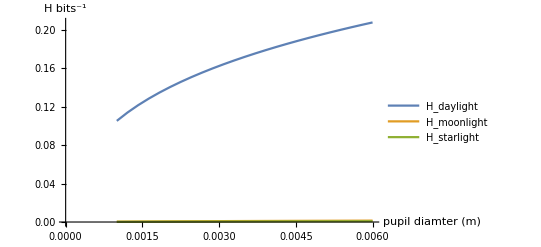

```mathematica
CoordDaylight=Transpose[{pupilValues,HDaylight}];
CoordMoonlight=Transpose[{pupilValues,HMoonlight}];
CoordStarlight=Transpose[{pupilValues,HStarlight}];
ListLinePlot[{CoordDaylight,CoordMoonlight,CoordStarlight},PlotLegends->{"H_daylight","H_moonlight","H_starlight"},AxesLabel->{"pupil diamter (m)","H bits^-1"}]
```